# RB-SFA: High Harmonic Generation in the Strong Field Approximation via Mathematica

© Emilio Pisanty 2014-2015. Licensed under GPL and CC-BY-SA.

## Usage and Examples

### Loading the package

You can use this software 
   ·  within the RB-SFA notebook itself by simply running the initialization cells of that notebook, or
   ·  from an external notebook by loading it as a package.
In the latter case, place a copy of the package file RB-SFA.m on the same directory as your notebook and run the loading command

```mathematica
Needs["RBSFA`",FileNameJoin[{NotebookDirectory[],"RB-SFA.m"}]]
```

You can also call the package from another directory by suitably modifying the directory call. If you plan on using this package in the long term you can use the File > Install prompt, in which case the package is simply loaded as Needs[“RBSFA`”], though this is not particularly recommended.

### Simple usage

For basic usage, simply call the main numerical integrator, makeDipoleList, with the vector potential you want to use, and provide any parameters you wish to specify using the FieldParameters option.

```mathematica
AbsoluteTiming[
simpleDipole=makeDipoleList[VectorPotential->Function[t,{F/ω Sin[ω t],0,0}],FieldParameters->{F->0.05,ω->0.057}];
]
```

{1.96916,Null}

Calling the function with insufficient parameters will produce error messages:

```mathematica
makeDipoleList[VectorPotential->Function[t,{F/ω Sin[ω t],0,0}]]
```

makeDipoleList::pot: The vector potential A provided as VectorPotential→Function[t, {F\ Sin[ω\ t]/ω, 0, 0}] is incorrect or is missing FieldParameters. Its usage as A[5.40412] returns {5.31906\ F, 0, 0} and should return a list of numbers.

$Aborted

The symbol ω is taken to be the carrier frequency, and is set by default to ω=0.057 atomic units, corresponding to a wavelength of 800 nm. If the carrier frequency is changed, this must be specified on both the field parameters and the explicit option for the integrator, as

```mathematica
makeDipoleList[VectorPotential->Function[t,{F/ω Sin[ω t],0,0}],FieldParameters->{F->0.05,ω->0.0456},CarrierFrequency->0.0456]
```

To see the spectrum, use the getSpectrum and the spectrumPlotter commands, such as

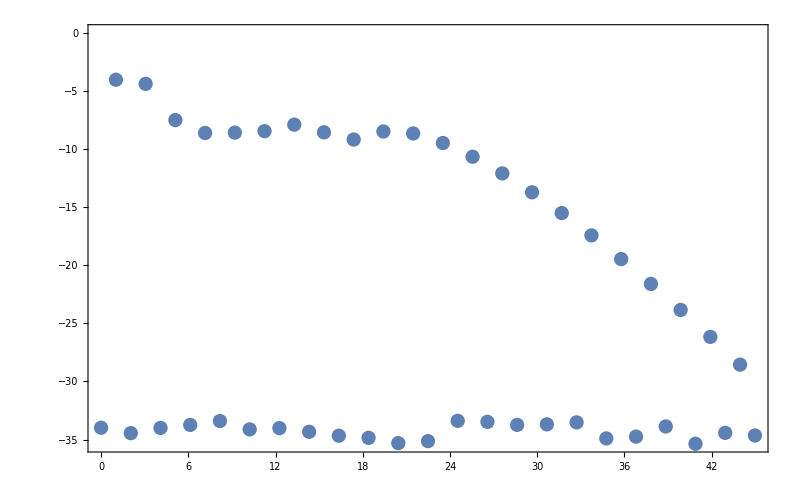

```mathematica
spectrumPlotter[getSpectrum[Most[simpleDipole]],Joined->False]
```

Note here the use of Most on the dipole when a monochromatic field is indicated. This ensures that the signal is actually periodic (i.e. it eliminates repetition between the initial and final points, which are separated by exactly one period). If this is not done, the spectrum is much noisier:

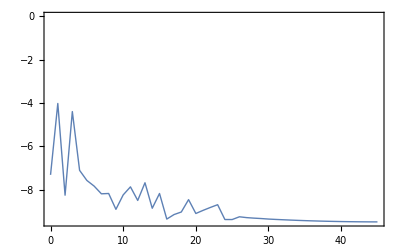

```mathematica
spectrumPlotter[getSpectrum[simpleDipole],ImageSize->400]
```

The default options are built for a periodic pulse for which simple functions of the vector potential can be integrated analytically, and for which only a single period of integration is necessary. More periods can be specified using the TotalCycles option. Similarly, the PointsPerCycle option controls the number of points per period.

```mathematica
AbsoluteTiming[
biggerDipole=makeDipoleList[VectorPotential->Function[t,{F/ω Sin[ω t],0,0}],FieldParameters->{F->0.05,ω->0.057},TotalCycles->4,PointsPerCycle->150];
]
```

{21.0118,Null}

To get a correct spectrum plot, give these settings to the spectrum plotter.

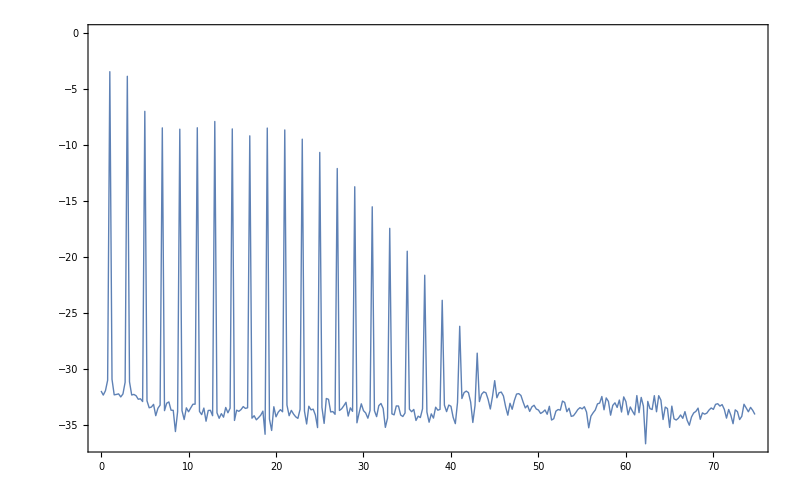

```mathematica
spectrumPlotter[getSpectrum[Most[biggerDipole]],TotalCycles->4,PointsPerCycle->150]
```

You can specify a Target chemical species using the option

```mathematica
?Target
```

Target is an option for makeDipoleList which specifies chemical species producing the HHG emission, pulling the ionization potential from the Wolfram ElementData curated data set.

i.e. using the syntax

```mathematica
heliumDipole=makeDipoleList[VectorPotential->Function[t,{F/ω Sin[ω t],0,0}],FieldParameters->{F->0.05,ω->0.057},Target->"Helium"];
xenonDipole=makeDipoleList[VectorPotential->Function[t,{F/ω Sin[ω t],0,0}],FieldParameters->{F->0.05,ω->0.057},Target->"Xenon"];
```

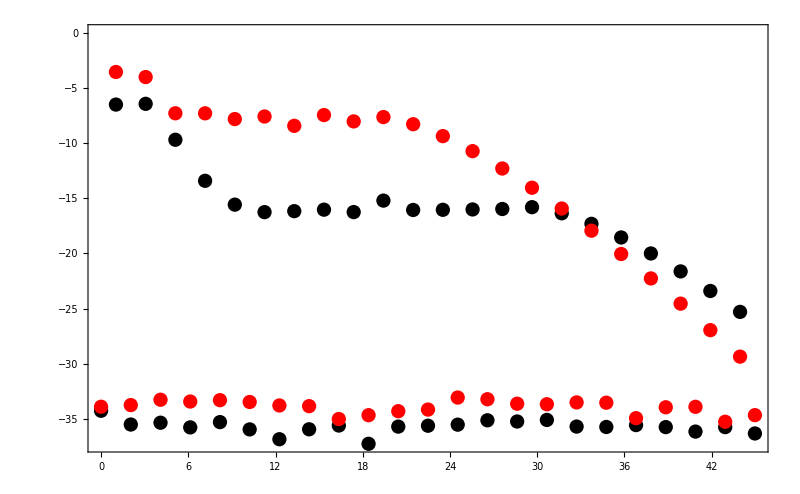

```mathematica
Show[{
spectrumPlotter[getSpectrum[Most[heliumDipole]],Joined->False,PlotStyle->Black],
spectrumPlotter[getSpectrum[Most[xenonDipole]],Joined->False,PlotStyle->Red]
}]
```

For convenience, the function getIonizationPotential gives a public-facing access to this functionality, via

```mathematica
?getIonizationPotential
```

getIonizationPotential[Target] returns the ionization potential of an atomic target, e.g. "Hydrogen", in atomic units.

getIonizationPotential[Target,q] returns the ionization potential of the q-th ion of the specified Target, in atomic units.

so that e.g.

```mathematica
{"H",#,UnitConvert[Quantity[#,"Hartrees"],"Electronvolts"]}&[getIonizationPotential["Hydrogen"]]
{"He^+",#,UnitConvert[Quantity[#,"Hartrees"],"Electronvolts"]}&[getIonizationPotential["Helium",1]]
```

{H,0.4997,13.6 eV}

{He^+,2.,54.42 eV}

An ionization potential can also be specified directly:

```mathematica
?IonizationPotential
```

IonizationPotential is an option for makeDipoleList which specifies the ionization potential I_p of the target.

To see the available options for this function (and others), use

```mathematica
Options[makeDipoleList]
```

{PointsPerCycle→90,TotalCycles→1,CarrierFrequency→0.057,VectorPotential→Automatic,FieldParameters→{},VectorPotentialGradient→None,Preintegrals→Analytic,ReportingFunction→Identity,Gate→SineSquaredGate[1/2],nGate→3/2,ϵCorrection→0.1,IonizationPotential→0.5,Target→Automatic,DipoleTransitionMatrixElement→hydrogenicDTME,PointNumberCorrection→0,Verbose→0}

All options have suitable information messages.

```mathematica
?VectorPotential
```

VectorPotential is an option for makeDipole list which specifies the field's vector potential. Usage should be VectorPotential→A, where A[t]//.pars must yield a list of numbers for numeric t and parameters indicated by FieldParameters→pars.

### Using numerical integration for the preintegrals

To simulate a pulse with an envelope, it can be convenient to perform the preintegrals numerically, using the option Preintegrals→”Numeric”. These cases are generally slower but mainly because they require many more periods of integration.

```mathematica
AbsoluteTiming[
numericallyIntegratedDipole=makeDipoleList[VectorPotential->Function[t,{F/ω envelope[t]Sin[ω t],0,0}],FieldParameters->{ω->0.057,F->0.055,envelope->cosPowerFlatTop[0.057,8,16]},TotalCycles->8,Preintegrals->"Numeric"];
]
```

{16.1751,Null}

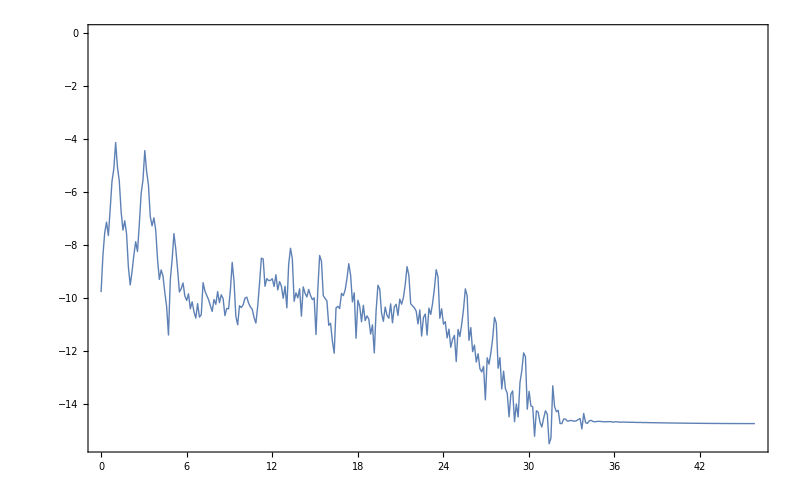

```mathematica
spectrumPlotter[getSpectrum[numericallyIntegratedDipole]]
```

When using flat top pulses, and other waveforms that depend on Piecewise functions, it is possible that the function will return errors caused by an Indeterminate derivative being evaluated at the corners of the envelope.

```mathematica
AbsoluteTiming[
flatTopPulseDipole=makeDipoleList[VectorPotential->Function[t,{F/ω envelope[t]Sin[ω t],0,0}],FieldParameters->{ω->0.057,F->0.055,envelope->flatTopEnvelope[0.057,8,2]},TotalCycles->8,Preintegrals->"Numeric"];
]
```

{17.7842,Null}

In these cases, use a numeric test to diagnose what’s happened

```mathematica
Tally[flatTopPulseDipole/._?NumberQ->✓]
```

{{{✓,✓,✓},721}}

and if the function is returning non-numeric values, it can help to fiddle with the PointNumberCorrection option.

```mathematica
?PointNumberCorrection
```

PointNumberCorrection is an option for makeDipole list which specifies an extra number of points to be integrated over, which is useful to prevent Indeterminate errors when a Piecewise envelope is being differentiated at the boundaries.

### Using the new numerical integration for the preintegrals

This section tests a NDSolve-based calculation of the preintegrals, using Preintegrals→”NewNumeric”. Currently very slow.

```mathematica
DateString[]
AbsoluteTiming[
numericallyIntegratedDipole=makeDipoleList[
VectorPotential->Function[t,{F/ω envelope[t]Sin[ω t],0,0}],
VectorPotentialGradient->Function[t,{{0,0,0},{0,0,0},{-(k F)/ω Sin[ω t],0,0}}],
FieldParameters->{ω->0.057,F->0.055,envelope->cosPowerFlatTop[0.057,8,16],k->ω/c,c->137}
,TotalCycles->8,Preintegrals->"Numeric"
]
]
DateString[]
```

Thu 4 Feb 2016 22:31:45

makeDipoleList::numnondip: The option Preintegrals→"Numeric" is currently unreliable when a vector potential is specified.

InterpolatingFunction::dmval: Input value {916.004} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {898.928} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

makeDipoleList::numnondip: The option Preintegrals→"Numeric" is currently unreliable when a vector potential is specified.

General::stop: Further output of makeDipoleList :: numnondip will be suppressed during this calculation.

-Graphics3D-

Thu 4 Feb 2016 22:31:49

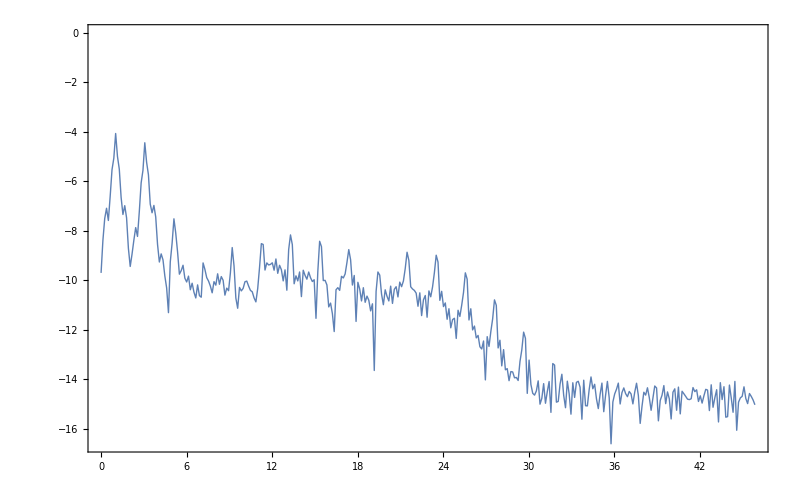

```mathematica
spectrumPlotter[getSpectrum[numericallyIntegratedDipole]]
```

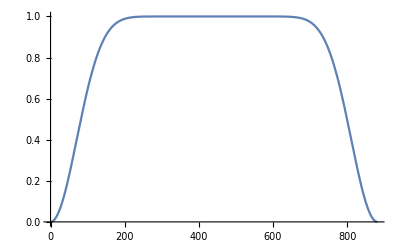

```mathematica
Plot[cosPowerFlatTop[0.057,8,16][t],{t,0,8 (2π)/0.057}]
```

### Parallelized environments

The numerical integration can be parallelized over via the use of ParallelTable and similar commands. Care must be taken to ensure that all parallel kernels have the package definitions available (using DistributeDefinitions, ParallelNeeds, or similar constructs). If a variable or function is used to store the results, this must be synchronized using SetSharedFunction or SetSharedVariable, as usual.

```mathematica
DistributeDefinitions["RBSFA`"];
SetSharedFunction[wavelengthScanDipole];

ParallelTable[
Print[AbsoluteTiming[
wavelengthScanDipole[λ]=makeDipoleList[VectorPotential->Function[t,{F/ω Sin[ω t],0,0}],FieldParameters->{F->0.05,ω->45.6/λ},CarrierFrequency->45.6/λ,PointsPerCycle->400];
]]
,{λ,800,1600,100}]
```

{65.3966,Null}

{67.5219,Null}

{67.9824,Null}

{68.8184,Null}

{70.7804,Null}

{70.9155,Null}

{71.6026,Null}

{43.4543,Null}

{41.8719,Null}

{Null,Null,Null,Null,Null,Null,Null,Null,Null}

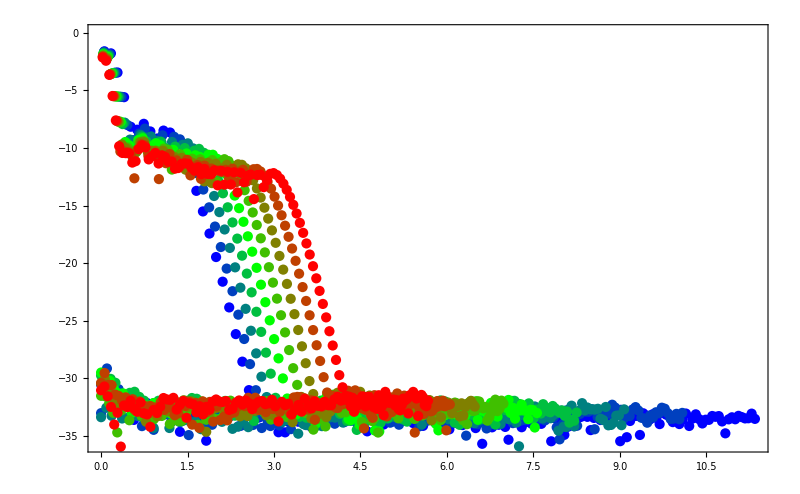

```mathematica
Show[Table[
spectrumPlotter[getSpectrum[Most[wavelengthScanDipole[λ]]],PlotStyle->Blend[{Blue,Green,Red},λ/800-1],CarrierFrequency->45.6/λ,Joined->False,FrequencyAxis->"Frequency",PointsPerCycle->400]
,{λ,800,1600,100}]]
```

### Writing output to file

For very large calculations (many integration points per cycle, in particular), the limiting factor is available memory. In these situations, it can help to write the data directly to a file on disk. This is slower (by a factor of about 2) but it has a roughly constant RAM footprint, so it enables calculations of a bigger size than would be possible otherwise. (Of course, this can also be done from non-parallelized calls!) This is done via the ReportingFunction option:

```mathematica
?ReportingFunction
```

ReportingFunction is an option for makeDipole list which specifies a function used to report the results, either internally (by the default, Identity) or to an external file.

In essence, the integration loop consists of a Table construct, which goes over the time t at which the integral is performed, and an inner integration construct. Setting an option ReportingFunction→f interposes the function  f  between these two steps, as

        Table[  f[  integrator[t]   ]    , {t, tInitial, tFinal}]

The default is f=Identity, which returns its input untouched, but it can also be replaced by a Write construct that can shunt its input to the hard disk without telling the kernel what it is, so it is not kept in memory.

```mathematica
Quit
```

```mathematica
DistributeDefinitions["RBSFA`"];
directory=NotebookDirectory[];
filename[F_]:=FileNameJoin[{directory,"Field scan data at F="<>ToString[F]<>".txt"}];

ParallelTable[
Print[AbsoluteTiming[
makeDipoleList[VectorPotential->Function[t,{F/ω Sin[ω t],0,0}],FieldParameters->{ω->0.057},CarrierFrequency->0.057,PointsPerCycle->400,
ReportingFunction->Function[Write[filename[F],#]]
];
]]
,{F,0.05,0.2,0.025}]
```

{66.2765,Null}

{68.2327,Null}

{68.4573,Null}

{69.0505,Null}

{69.6457,Null}

{69.8211,Null}

{70.4778,Null}

{Null,Null,Null,Null,Null,Null,Null}

The data in the files can then be pulled in quite simply using e.g.

```mathematica
Do[  intensityScanDipole[F]=ReadList[filename[F]],{F,0.05,0.2,0.025}]
```

This tends to litter the directories by creating lots of files for different parameters, so it is usually cleaner to Save them into a single file, e.g. using

```mathematica
Save[FileNameJoin[{NotebookDirectory[],"Field scan collected data.txt"}],intensityScanDipole]
```

which in turn can then be pulled in using

```mathematica
<<(FileNameJoin[{NotebookDirectory[],"Field scan collected data.txt"}]);
```

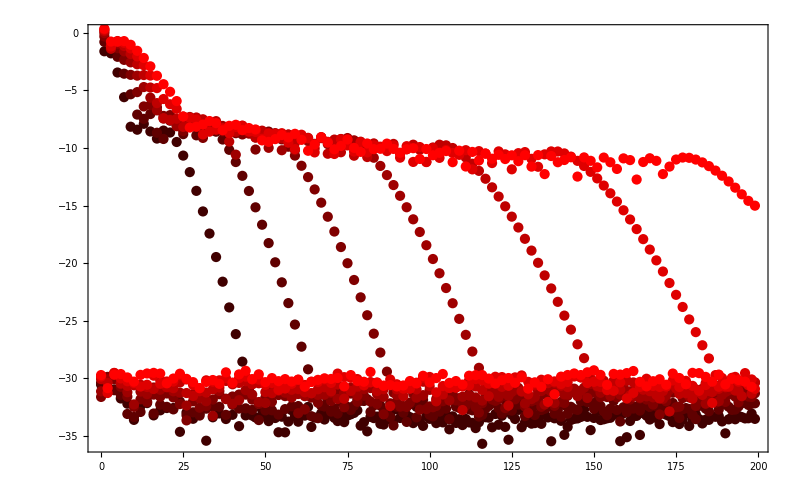

```mathematica
Show[Table[
spectrumPlotter[getSpectrum[Most[intensityScanDipole[F]]],CarrierFrequency->0.057,Joined->False,PointsPerCycle->400,PlotStyle->Blend[{Black,Red},F/0.2]]
,{F,0.05,0.2,0.025}]]
```

As written, though, this has the disadvantage that each subkernel must access the hard drive for every timestep of the computation, which obviously responsible for (at least most of) the slowdown. A middle ground is also possible by choosing an appropriate ReportingFunction: a function which will cache a specific number k of results on RAM, and then write them to file all in one go. This is on the development to do (wish) list, and will hopefully be implemented soon - if time allows.

### Time and memory use

The benchmarks below were taken on a desktop machine with 8-thread, 4-core Intel i7-3770 CPU at 3.40GHz, 16GB RAM, running Mathematica 10.0.1 over Ubuntu 14.04. The time taken per computation depends most strongly on the PointsPerCycle used to sample and integrate, and the dependence is therefore quadratic.

```mathematica
timingsList=Table[
{n,AbsoluteTiming[MaxMemoryUsed[makeDipoleList[VectorPotential->Function[t,{F/ω Sin[ω t],0,0}],FieldParameters->{F->√(n/100)0.053,ω->0.057},PointsPerCycle->n]]]}
,{n,100,1000,100}]
```

{{100,{2.36167,4905296}},{200,{9.40602,19018888}},{300,{20.6878,43497000}},{400,{37.2461,78976528}},{500,{57.5847,118770848}},{600,{82.7101,173233496}},{700,{112.082,232621352}},{800,{150.096,301125912}},{900,{187.298,387140808}},{1000,{233.122,473885368}}}

#### Timings

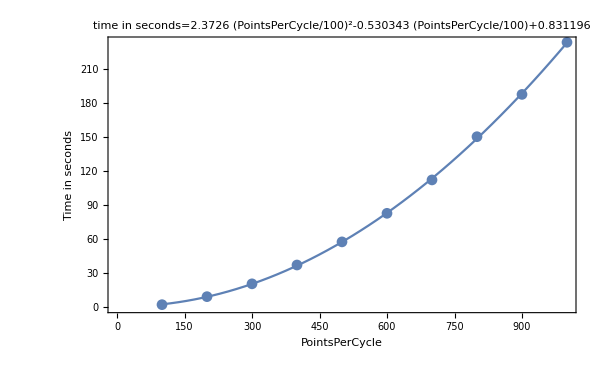

```mathematica
timingsModel=LinearModelFit[(Flatten/@timingsList)⟦All,{1,2}⟧,{1,n,n^2},{n}];
Show[{
ListPlot[
(Flatten/@timingsList)⟦All,{1,2}⟧
],
Plot[timingsModel[n],{n,timingsList⟦1,1⟧,timingsList⟦-1,1⟧}]
}
,Frame->True,PlotLabel->Row[{"time in seconds=",timingsModel[100"(PointsPerCycle/100)"]}],FrameLabel->{"PointsPerCycle","Time in seconds"},ImageSize->600
]
```

#### Maximum memory used

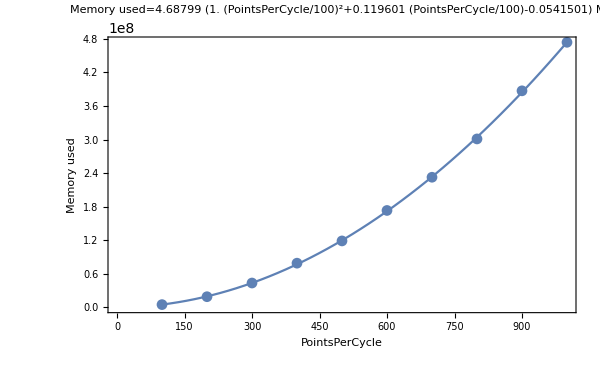

```mathematica
memoryModel=LinearModelFit[(Flatten/@timingsList)⟦All,{1,3}⟧,{1,n,n^2},{n}];
Show[{
ListPlot[
(Flatten/@timingsList)⟦All,{1,3}⟧
],
Plot[memoryModel[n],{n,timingsList⟦1,1⟧,timingsList⟦-1,1⟧}]
}
,Frame->True,PlotLabel->Row[{"Memory used=",Simplify[memoryModel[100."(PointsPerCycle/100)"] 10^-6"MB"]}],FrameLabel->{"PointsPerCycle","Memory used"},ImageSize->600
]
```

#### In parallel

Inside parallel environments the timings are somewhat slower, by a factor of about 1.8. The timings below were taken with 7 Mathematica kernels running in parallel.

```mathematica
DistributeDefinitions["RBSFA`"];
```

```mathematica
parallelTimingsList=ParallelTable[
{n,AbsoluteTiming[MaxMemoryUsed[makeDipoleList[VectorPotential->Function[t,{F/ω Sin[ω t],0,0}],FieldParameters->{F->√(n/100)0.053,ω->45.6/λ},CarrierFrequency->45.6/λ,PointsPerCycle->n]]]}
,{λ,770,830,10},{n,100,1000,100}]
```

{{{100,{4.71833,7949312}},{200,{18.2567,19028920}},{300,{39.6818,43507248}},{400,{68.0825,75529984}},{500,{108.27,118772272}},{600,{154.871,173234856}},{700,{211.182,232622488}},{800,{275.072,301126208}},{900,{350.061,387140984}},{1000,{424.31,473885664}}},{{100,{3.7169,7949264}},{200,{17.4824,19028912}},{300,{40.1556,43507248}},{400,{68.1348,75529984}},{500,{109.399,118772272}},{600,{153.631,173234976}},{700,{211.956,232622248}},{800,{279.29,301126208}},{900,{353.1,387141104}},{1000,{429.039,473885664}}},{{100,{4.70831,7949264}},{200,{17.3451,19028912}},{300,{40.1826,43507248}},{400,{68.9951,75529984}},{500,{109.87,118772272}},{600,{156.143,173234976}},{700,{209.361,232622488}},{800,{279.29,301126208}},{900,{350.784,387141104}},{1000,{418.914,473885664}}},{{100,{4.27991,7949264}},{200,{18.6273,19028912}},{300,{40.4553,43507248}},{400,{67.5833,75529984}},{500,{107.493,118772272}},{600,{151.738,173234976}},{700,{211.565,232622368}},{800,{276.237,301126208}},{900,{352.376,387141104}},{1000,{429.842,473885664}}},{{100,{4.80072,7949264}},{200,{17.9797,19028912}},{300,{38.2944,43507248}},{400,{68.7844,75529984}},{500,{105.406,118772272}},{600,{151.986,173234976}},{700,{216.018,232622488}},{800,{279.116,301126208}},{900,{361.033,387141104}},{1000,{424.589,473885664}}},{{100,{4.24956,7949264}},{200,{17.1782,19028912}},{300,{40.1991,43507248}},{400,{67.2693,75529864}},{500,{108.852,118772032}},{600,{156.147,173234736}},{700,{210.96,232622008}},{800,{279.971,301126208}},{900,{352.399,387141104}},{1000,{423.345,473885664}}},{{100,{4.4809,7949264}},{200,{17.6272,19028912}},{300,{39.652,43507248}},{400,{67.7538,75529984}},{500,{107.413,118772272}},{600,{156.833,173234976}},{700,{213.902,232622488}},{800,{276.711,301126208}},{900,{352.447,387140984}},{1000,{423.858,473885544}}}}

```mathematica
parallelTimingsListAveraged=Table[{parallelTimingsListᵀ⟦k,1,1⟧,Mean[ parallelTimingsListᵀ⟦k,All,2⟧]},{k,Length[parallelTimingsListᵀ]}]
```

{{100,{4.42209,55644896/7}},{200,{17.7852,133202392/7}},{300,{39.803,43507248}},{400,{68.0862,528709768/7}},{500,{108.101,831405664/7}},{600,{154.479,1212644472/7}},{700,{212.135,232622368}},{800,{277.955,301126208}},{900,{353.171,2709987488/7}},{1000,{424.842,3317199528/7}}}

Timings

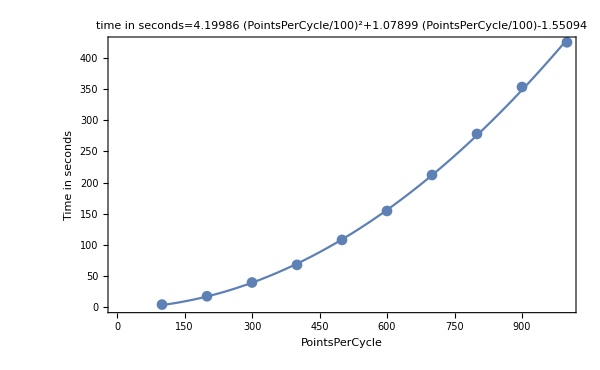

```mathematica
parallelTimingsModel=LinearModelFit[(Flatten/@parallelTimingsListAveraged)⟦All,{1,2}⟧,{1,n,n^2},{n}];
Show[{
ListPlot[
(Flatten/@parallelTimingsListAveraged)⟦All,{1,2}⟧
],
Plot[parallelTimingsModel[n],{n,parallelTimingsListAveraged⟦1,1⟧,parallelTimingsListAveraged⟦-1,1⟧}]
}
,Frame->True,PlotLabel->Row[{"time in seconds=",parallelTimingsModel[100"(PointsPerCycle/100)"]}],FrameLabel->{"PointsPerCycle","Time in seconds"},ImageSize->600
]
```

Memory

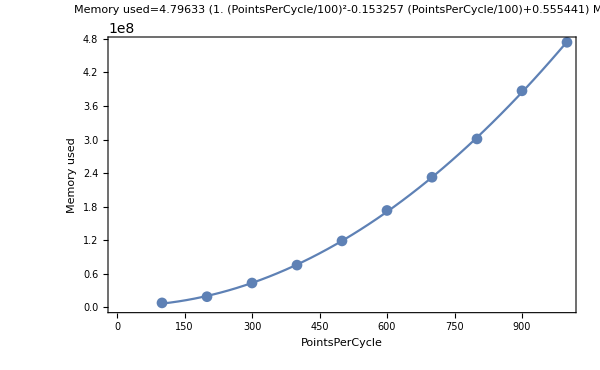

```mathematica
parallelMemoryModel=LinearModelFit[(Flatten/@parallelTimingsListAveraged)⟦All,{1,3}⟧,{1,n,n^2},{n}];
Show[{
ListPlot[
(Flatten/@parallelTimingsListAveraged)⟦All,{1,3}⟧
],
Plot[parallelMemoryModel[n],{n,parallelTimingsListAveraged⟦1,1⟧,parallelTimingsListAveraged⟦-1,1⟧}]
}
,Frame->True,PlotLabel->Row[{"Memory used=",Simplify[parallelMemoryModel[100."(PointsPerCycle/100)"] 10^-6"MB"]}],FrameLabel->{"PointsPerCycle","Memory used"},ImageSize->600
]
```

### Cutting off the long trajectories

This section shows, as an example of the use of the package, the use of the integration gate to eliminate the contribution from long trajectories. This can be tested by the reduced presence of quantum path interference patterns in the spectrum, and more practically by examining the dependence of the quantum phase on the field intensity.

#### The gating cutoff time

Given the classical trajectory,

```mathematica
trajectory[ωt_,ωt0_]:=(x[ωt]/.First@DSolve[
{x''[ωt]==Cos[ωt],x'[ωt0]==0,x[ωt0]==0}
,x,ωt
])
```

the recollision kinetic energy and excursion time can be found as

```mathematica
recollisionKE[ωt0_?NumericQ]:=(D[trajectory[ωtt,ωt0],ωtt]^2/.ωtt->ωt)/.First[Quiet[NSolve[{trajectory[ωt,ωt0]==0,π/2≤ωt<2π},ωt]]]
recollisionExcursionTime[ωt0_?NumericQ]:=(ωt-ωt0)/.First[Quiet[NSolve[{trajectory[ωt,ωt0]==0,π/2≤ωt<2π},ωt]]]
```

and the excursion time at the cutoff can be found by maximizing the kinetic energy.

```mathematica
FindMaximum[recollisionKE[ωt0],{ωt0,0.3}]
recollisionExcursionTime[ωt0]/(2π)/.Last[%]
```

{1.58657,{ωt0→0.313408}}

0.650239

In other words, the cutoff trajectories occur at excursion times of ω τ=0.65×2π, i.e. at a gate number of 0.65 cycles.

#### Calculation

This calculation runs a standard linearly-polarized field with intensity between 0.8 and 2×10^14 W/cm^2, with a fine intensity resolution. We compare the standard, non-gated calculation against a calculation with nGate set to 0.65, as per the above, and a sharp sin^2 cutoff of 0.05 cycles.

```mathematica
intRange=Range[0.8,2.,0.002];
nppsl=150;
SetSharedFunction[quantumPhaseScan,fourierDipole];
LaunchKernels[];
DistributeDefinitions["RBSFA`"];
nFlat=0.65;
nGateRamp=0.05;
```

The actual calculation,

```mathematica
DateString[]
AbsoluteTiming[
ParallelTable[
quantumPhaseScan[trajectories,int]=makeDipoleList[
VectorPotential->Function[t,{F/ω Sin[ω t],0,0}],
FieldParameters->{F->√int 0.053,ω->0.057},
PointsPerCycle->nppsl,
If[trajectories==="Short",Sequence@@{Gate->SineSquaredGate[nGateRamp],nGate->(nFlat+nGateRamp)},##&[],##&[]]
];
,{int,intRange},{trajectories,{"Short","Long"}}];
]
DateString[]
```

Wed 2 Dec 2015 19:28:50

{1216.8,Null}

Wed 2 Dec 2015 19:49:07

and the energy-domain dipole.

```mathematica
AbsoluteTiming[
Table[
fourierDipole[trajectories,int]=Fourier[
Re[quantumPhaseScan[trajectories,int]⟦1;;-2,1⟧]
,FourierParameters->{-1, 1}];
,{int,intRange},{trajectories,{"Short","Long"}}];
]
```

{0.093762,Null}

#### Analysis

```mathematica
Block[{background},
background=ListLogPlot[
Flatten[Table[
{Range[0,nppsl/2-1],Abs[fourierDipole[trajectories,m[intRange]]⟦1;;nppsl/2⟧]^2}ᵀ
,{m,{Min,Max}},{trajectories,{"Short","Long"}}],1]
,ImageSize->420
,PlotStyle->{{Red,Opacity[0.5]},{Blue,Opacity[0.5]},{Red},{Blue}}
,PlotLabel->"Harmonic dipole, Short vs Long;\nsolid at "<>ToString[Max[intRange]]<>"×10^14 W/cm^2 pale at "<>ToString[Min[intRange]]<>"×10^14 W/cm^2."
,FrameLabel->{"Harmonic order",""}
,Frame->True
];
SlideView[Table[
Row[{
Show[{
RegionPlot[Abs[ϕ]>1,{int,Min[intRange],Max[intRange]},{ϕ,-1.2,1.2},PlotStyle->GrayLevel[0.9],Method->{"AxesInFront"->False},BoundaryStyle->None],
ListPlot[
Table[
Flatten[Table[
{#,{#⟦1⟧,#⟦2⟧+2},{#⟦1⟧,#⟦2⟧-2}}&@{int,1/π Arg[fourierDipole[trajectories,int]⟦HO+1⟧]}
,{int,intRange⟦1;;-1⟧}],1]
,{trajectories,{"Short","Long"}}]
,PlotStyle->{{PointSize[0.01],Red},{PointSize[0.01],Blue}}
,Joined->False
]
}
,PlotRange->1.2{-1,1},AspectRatio->0.6
,PlotRangePadding->{None,Automatic}
,Axes->True
,ImageSize->450
,PlotLabel->"H"<>ToString[HO]<>" phase, Short vs Long"
,FrameLabel->{"Intensity/10^14 W cm^-2","Harmonics phase/π"}
],
Show[{background},GridLines->{{HO},None}]
}]
,{HO,1,nppsl/2,2}],7]
]
```

The short- and long-trajectory calculations are in red and blue respectively. It is clear that, in the plateau regions, the gated calculation has a much smoother dependence of the harmonic phase on the field intensity. On the other hand, the cutoff is perfectly preserved. These are the hallmarks that the contributions from long trajectories have been mostly eliminated.

### Nondipole contributions

Nondipole contributions can be specified by setting a nonzero vector potential gradient:

```mathematica
?VectorPotentialGradient
```

"VectorPotentialGradient is an option for makeDipole list which specifies the gradient of the field's vector potential. Usage should be VectorPotentialGradient→GA, where GA[t]//.pars must yield a square matrix of the same dimension as the vector potential for numeric t and parameters indicated by FieldParameters→pars. The indices must be such that GA[t]⟦i,j⟧ returns ∂_i A_j[t]."

If, for example, the travelling-wave form of the vector potential is of the form A(r,t)=F/ω x̂ cos(k z-ω t), then at the origin the vector potential is A(0,t)=F/ω x̂ cos(ω t) and it has a single nonzero entry in its gradient matrix ∇A, i.e. ∂_z A_x=-(k F)/ωsin(ωt). This is entered into the VectorPotentialGradient option as

```mathematica
nonDipoleContributions=makeDipoleList[
VectorPotential->Function[t,{F/ω Cos[ω t],0,0}],
VectorPotentialGradient->Function[t,{{0,0,0},{0,0,0},{-(k F)/ω Sin[ω t],0,0}}],
FieldParameters->{F->0.05,ω->0.057,k->ω/c,c->137}
];
```

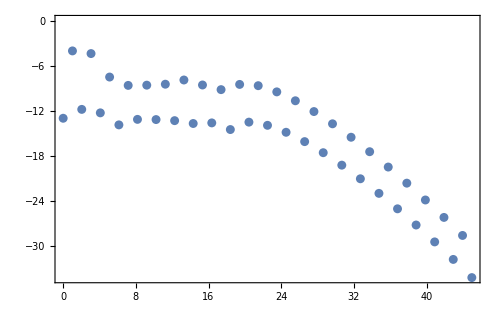

```mathematica
spectrumPlotter[getSpectrum[Most[nonDipoleContributions]],Joined->False,ImageSize->500]
```

At low wavelengths, the first obvious effect is the appearance of even harmonics. This is the expected behaviour, with the harmonics along the laser propagation direction. (Informally, the magnetic pushing on the wavepacket acts on the propagation direction on both halves of each laser period. This off-axis recollision causes the dipole to oscillate in the propagation direction with an even symmetry. More formally, the dynamical symmetries of the problem permit even (but not odd) harmonics along this direction.) This is indeed what is observed:

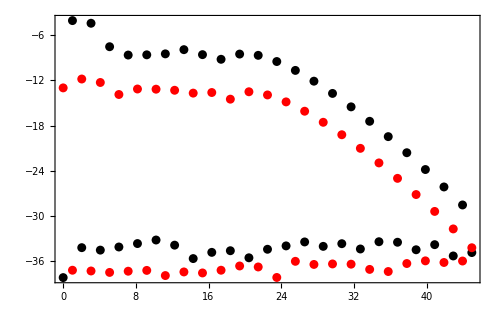

```mathematica
Show[{
spectrumPlotter[getSpectrum[nonDipoleContributions⟦1;;-2,{1,2}⟧],Joined->False,PlotStyle->Black],
spectrumPlotter[getSpectrum[nonDipoleContributions⟦1;;-2,{3}⟧],Joined->False,PlotStyle->Red]
},PlotRange->All,ImageSize->500]
```

### Benchmarking the nondipole contributions

#### Nondipole contributions in a crossed-beam setup

This section explores the harmonic emission by a crossed-beam setup, with nondipole contributions, as a benchmarking step for the latter. The crossed-beam setup was proposed by X.-M. Tong and S.-I. Chu in Phys. Rev. A 58 no .4, R2656 (1998), and it was explored in a nondipole setting by V. Averbukh et al. in Phys Rev. A 65, 063402 (2002). The results below reproduce those of Averbukh et al.

In short, we consider the harmonic emission by a circularly polarized pulse propagating along the z direction, at frequency ω, and a linearly polarized pulse of frequency r ω propagating along the x direction and polarized along the z direction.

```mathematica
(crossedBeamsA[x_,z_]=Function[t,
{F1/ω Cos[k z-ω t],F1/ω Sin[k z-ω t],F2/(r ω)Sin[r k x-r ω t+θ0]}
])[t]//MatrixForm
(crossedBeamsGA[x_]=Function[t,Evaluate[{
D[crossedBeamsA[x,z][t],x]/.{z->0},
D[crossedBeamsA[x,z][t],y]/.{z->0},
D[crossedBeamsA[x,z][t],z]/.{z->0}
}]]
)[t]//MatrixForm
```

((F1 Cos[k z-t ω])/ω
(F1 Sin[k z-t ω])/ω
(F2 Sin[k r x+θ0-r t ω])/(r ω))

(0 | 0 | (F2 k Cos[k r x+θ0-r t ω])/ω
0 | 0 | 0
(F1 k Sin[t ω])/ω | (F1 k Cos[t ω])/ω | 0)

The dipole selection rules allow harmonic orders of the form 2r ℓ±1, with ℓ=0,1,2,3,..., with polarization in the x,y plane, and harmonics of order r(2ℓ+1), with ℓ=0,1,2,3,..., polarized along the z direction.

```mathematica
allowedHarmonics[r_,{1,2}]:=Select[Union[2r Range[0,100]+1,2r Range[0,100]-1],#>0&]
allowedHarmonics[r_,{3}]:=r(2Range[0,100]+1)
```

For the calculation, then, some preliminaries,

```mathematica
αRange={0,1/137};
nppcb=240;
crossedBeamsParameters[rr_]:={F1->0.1,F2->0.2,ω->0.057,θ0->0,r->rr,k->α ω};
DistributeDefinitions["RBSFA`"];
SetSharedFunction[crossedBeamsResults];
```

and the calculation itself for r=2 and r=5.

```mathematica
Print[DateString[]]
ParallelTable[AbsoluteTiming[
crossedBeamsResults[r,α]=makeDipoleList[
VectorPotential->crossedBeamsA[0,0],VectorPotentialGradient->crossedBeamsGA[0],FieldParameters->crossedBeamsParameters[r]
,DipoleTransitionMatrixElement->Function[{p,κ},gaussianDTME[p,1/1.3]]
,CarrierFrequency->0.057,PointsPerCycle->nppcb
];
],{r,{2,5}},{α,αRange}]
Print[DateString[]]
```

Thu 1 Oct 2015 15:42:15

{{{29.6518,Null},{34.7323,Null}},{{28.9947,Null},{34.9678,Null}}}

Thu 1 Oct 2015 15:43:20

Results for r=2, comparable to Fig. 1 in Averbukh et al. Dashed lines mark the dipole-allowed harmonics. The left-hand column has nondipole contributions turned off (α=0), and the right-hand column includes the nondipole contributions and observes a massive increase in the amplitude of the dipole-forbidden harmonics.

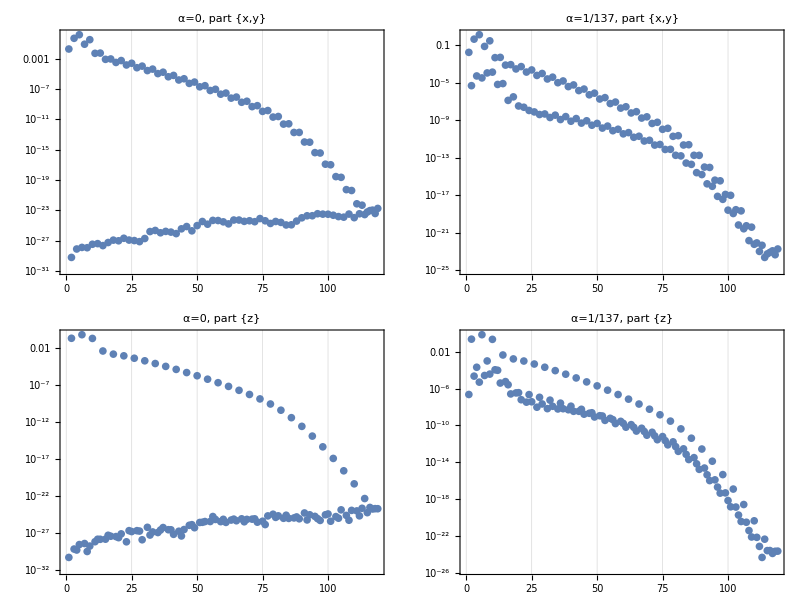

```mathematica
Grid[Table[
ListLogPlot[
getSpectrum[crossedBeamsResults[2,α]⟦1;;-2,part⟧,ωPower->2]⟦2;;⟧
,Joined->False,ImageSize->600,PlotTheme->"Detailed",PlotRange->Full
,GridLines->{allowedHarmonics[2,part],None}
,PlotLabel->Row[{"α=",α,", part ",{"x","y","z"}⟦part⟧}]
],{part,{{1,2},{3}}},{α,αRange}]]
```

Results for r=5, comparable to Fig. 2 in Averbukh et al.

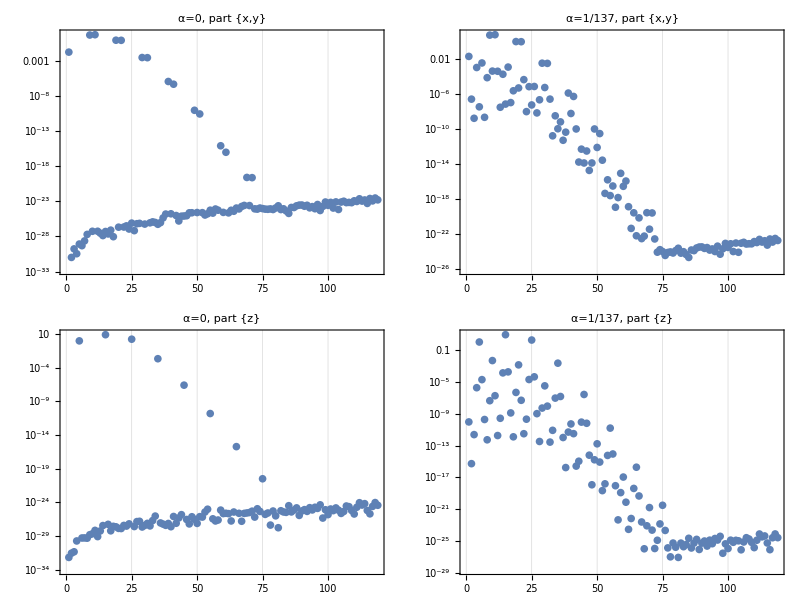

```mathematica
Grid[Table[
ListLogPlot[
getSpectrum[crossedBeamsResults[5,α]⟦1;;-2,part⟧,ωPower->2]⟦2;;⟧
,Joined->False,ImageSize->600,PlotTheme->"Detailed",PlotRange->Full
,GridLines->{allowedHarmonics[5,part],None}
,PlotLabel->Row[{"α=",α,", part ",{"x","y","z"}⟦part⟧}]
],{part,{{1,2},{3}}},{α,αRange}]]
```

#### Multiple plateaus in HHG in ions

This section benchmarks this code against the results of N.J. Kylstra et al. reported in J. Phys B: At. Mol. Opt. Phys. 34 no. 3, L55 (2001);. In particular,  we study HHG in the He^+ ion at high intensity (I=5.6×10^15 W cm^-2) and reasonable (800nm) wavelength.

```mathematica
(kylstraA[z_]=Function[t,{F/ω Sin[(ω t-k z)/4]^2 Sin[ω t-k z],0,0}])[t]//MatrixForm
(kylstraGA=Function[t,Evaluate[{
D[kylstraA[z][t],x]/.{z->0},
D[kylstraA[z][t],y]/.{z->0},
D[kylstraA[z][t],z]/.{z->0}
}]]
)[t]//MatrixForm
```

(-(F Sin[k z-t ω] Sin[1/4 (-k z+t ω)]^2)/ω
0
0)

(0 | 0 | 0
0 | 0 | 0
-(F k Cos[t ω] Sin[(t ω)/4]^2)/ω-(F k Cos[(t ω)/4] Sin[(t ω)/4] Sin[t ω])/(2 ω) | 0 | 0)

```mathematica
nppk=1500;
```

```mathematica
DateString[]
AbsoluteTiming[
kylstraTest=makeDipoleList[
VectorPotential->kylstraA[0],VectorPotentialGradient->kylstraGA,
FieldParameters->{F->√(5.6 10^15/10^14)0.053,ω->0.057,k->α ω,α->1/137},IonizationPotential->2,
PointsPerCycle->nppk,TotalCycles->2
];
]
DateString[]
```

Thu 1 Oct 2015 18:25:47

{1619.16,Null}

Thu 1 Oct 2015 18:52:46

Plotting the results. The x component (along the laser polarization) is in black, the z component (along the laser propagation) is in red.

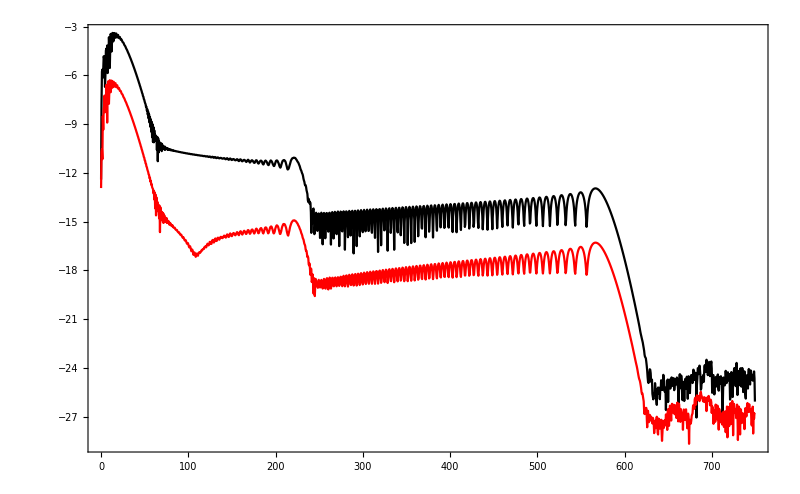

```mathematica
Show[
Table[
spectrumPlotter[getSpectrum[kylstraTest⟦1;;-2,part⟧,ωPower->2],Joined->True,PointsPerCycle->nppk,TotalCycles->2,PlotStyle->(part/.{{1,2}->Black,{3}->Red})]
,{part,{{1},{3}}}]
,PlotRange->All
]
```

The results are a good qualitative match to the dipoles reported by Kylstra et al., with the notable exception of the low-order harmonics below n≲50.

On the other hand, taken naively this code cannot be applied to the harder targets described in that paper (Li^(2+) and Be^(3+), at intensities between 0.9 and 3.6×10^17 W cm^-2), which have cutoffs of order as high as 35000, which requires several days to several months of calculation using the naive scaling. (That said, using a smarter choice of ReportingFunction, judicious use of parallelization and lots of waiting, those targets are probably within reach of this code.)

### Perodicity of nondipole contributions

```mathematica
Quit
```

```mathematica
(crossedBeamsA[t_]=First/@Sum[
F/ω({{Cos[θ]}, {0}, {-s Sin[θ]}})Cos[k{s Sin[θ],0,Cos[θ]}.{x,y,z}-ω t-s ϕ]
,{s,{-1,1}}])//MatrixForm;
(crossedBeamsGA[t_]=Evaluate[{
D[crossedBeamsA[t],x],
D[crossedBeamsA[t],y],
D[crossedBeamsA[t],z]
}])//MatrixForm;
crossedBeamsParameters={x->0,y->0,z->0,F->√0.5 0.053,ω->0.057,θ->10.°,k->α ω};
```

```mathematica
DateString[]
Table[
First[AbsoluteTiming[
symmetryTestDipole[α,ϕ]=makeDipoleList[
VectorPotential->crossedBeamsA,VectorPotentialGradient->crossedBeamsGA,FieldParameters->crossedBeamsParameters,
PointsPerCycle->160
];
]]
,{α,{0,1/137}},{ϕ,{0,30°}}]
DateString[]
```

Fri 16 Oct 2015 12:09:53

{{5.97834,6.65576},{8.31512,11.9895}}

Fri 16 Oct 2015 12:10:26

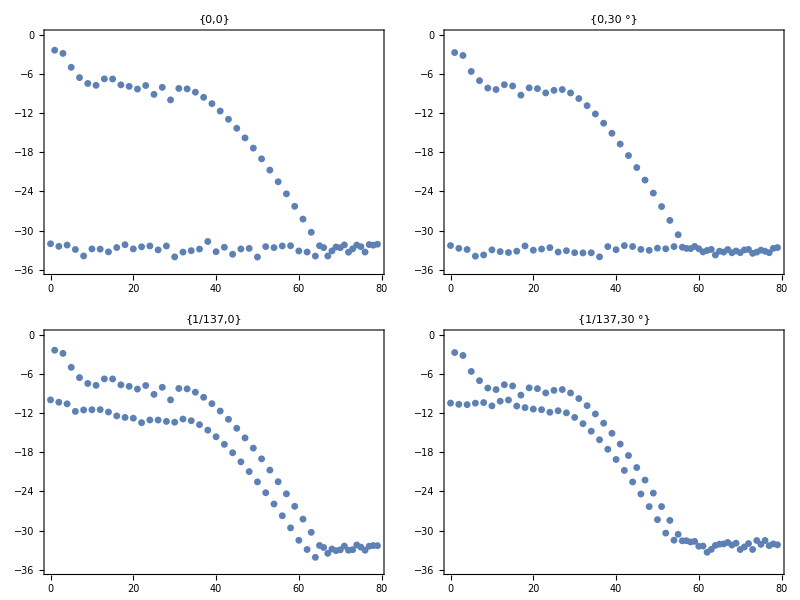

```mathematica
Grid[Table[
spectrumPlotter[
getSpectrum[symmetryTestDipole[α,ϕ]⟦1;;-2,{1,2,3}⟧]
,Joined->False,PointsPerCycle->160,ImageSize->450,PlotLabel->{α,ϕ},PlotRange->{-36,0}
]
,{α,{0,1/137}},{ϕ,{0,30°}}]]
```

Compare this with the unacceptably high noise floor from the previous version for the case α=1/137, ϕ=30°.

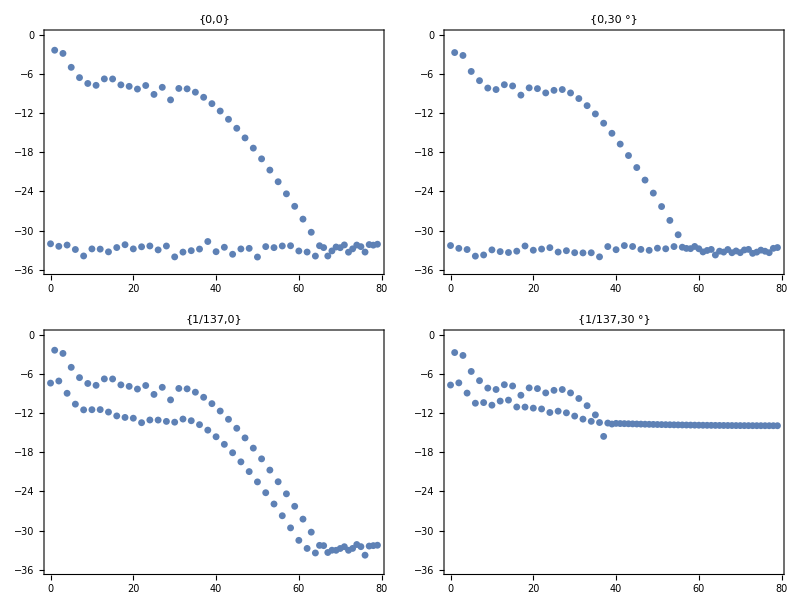

### Debugging and benchmarking tools

If something goes funny with your calls, then before you start taking makeDipoleList apart you can try using its Verbose option to diagnose the internal functions it is using. In particular:

Setting Verbose→1 makes makeDipoleList print the Information of the key internal functions it is using, before it goes on to the integration loop.

```mathematica
makeDipoleList[VectorPotential->Function[t,{F/ω Sin[ω t],0,0}],FieldParameters->{F->0.05,ω->0.057},Verbose->1]⟦1;;10⟧
```

RBSFA`Private`A

RBSFA`Private`A[RBSFA`Private`t$_]={0.877193 Sin[0.057 RBSFA`Private`t$],0,0}

RBSFA`Private`GA

RBSFA`Private`GA[RBSFA`Private`t$_]={{0,0,0},{0,0,0},{0,0,0}}

RBSFA`Private`ps

RBSFA`Private`ps[RBSFA`Private`t_?RBSFA`Private`gridPointQ,RBSFA`Private`tt_?RBSFA`Private`gridPointQ]:=RBSFA`Private`ps[RBSFA`Private`t,RBSFA`Private`tt]=-(Inverse[IdentityMatrix[Length[RBSFA`Private`A[RBSFA`Private`tInit]]]-(RBSFA`Private`GAIntInt[RBSFA`Private`t,RBSFA`Private`tt]+Transpose[RBSFA`Private`GAIntInt[RBSFA`Private`t,RBSFA`Private`tt]])/(RBSFA`Private`t-RBSFA`Private`tt-ⅈ RBSFA`Private`ϵ)].(RBSFA`Private`AInt[RBSFA`Private`t,RBSFA`Private`tt]-RBSFA`Private`bigPScorrectionInt[RBSFA`Private`t,RBSFA`Private`tt])/(RBSFA`Private`t-RBSFA`Private`tt-ⅈ RBSFA`Private`ϵ))

RBSFA`Private`pi

RBSFA`Private`pi[RBSFA`Private`p_,RBSFA`Private`t_]:=RBSFA`Private`p+RBSFA`Private`A[RBSFA`Private`t]-RBSFA`Private`GAInt[RBSFA`Private`t].RBSFA`Private`p-RBSFA`Private`GAdotAInt[RBSFA`Private`t]

RBSFA`Private`S

RBSFA`Private`S[RBSFA`Private`t_?RBSFA`Private`gridPointQ,RBSFA`Private`tt_?RBSFA`Private`gridPointQ]:=1/2 (Norm[RBSFA`Private`ps[RBSFA`Private`t,RBSFA`Private`tt]]^2+(RBSFA`Private`κ)^2) (RBSFA`Private`t-RBSFA`Private`tt)+RBSFA`Private`ps[RBSFA`Private`t,RBSFA`Private`tt].RBSFA`Private`AInt[RBSFA`Private`t,RBSFA`Private`tt]+1/2 RBSFA`Private`A2Int[RBSFA`Private`t,RBSFA`Private`tt]-(RBSFA`Private`ps[RBSFA`Private`t,RBSFA`Private`tt].RBSFA`Private`GAIntInt[RBSFA`Private`t,RBSFA`Private`tt].RBSFA`Private`ps[RBSFA`Private`t,RBSFA`Private`tt]+RBSFA`Private`ps[RBSFA`Private`t,RBSFA`Private`tt].RBSFA`Private`bigPScorrectionInt[RBSFA`Private`t,RBSFA`Private`tt]+RBSFA`Private`AdotGAdotAInt[RBSFA`Private`t,RBSFA`Private`tt])

RBSFA`Private`AInt

RBSFA`Private`AInt[RBSFA`Private`t$_]={-15.3894 Cos[0.057 RBSFA`Private`t$],0,0}
 
RBSFA`Private`AInt[RBSFA`Private`t$_,RBSFA`Private`tt$_]={15.3894 Cos[0.057 RBSFA`Private`tt$]-15.3894 Cos[0.057 RBSFA`Private`t$],0,0}

RBSFA`Private`A2Int

RBSFA`Private`A2Int[RBSFA`Private`t$_]=0.769468 (0.5 RBSFA`Private`t$-4.38596 Sin[0.114 RBSFA`Private`t$])
 
RBSFA`Private`A2Int[RBSFA`Private`t$_,RBSFA`Private`tt$_]=-0.769468 (0.5 RBSFA`Private`tt$-4.38596 Sin[0.114 RBSFA`Private`tt$])+0.769468 (0.5 RBSFA`Private`t$-4.38596 Sin[0.114 RBSFA`Private`t$])

RBSFA`Private`GAInt

RBSFA`Private`GAInt[RBSFA`Private`t$_]={{0,0,0},{0,0,0},{0,0,0}}
 
RBSFA`Private`GAInt[RBSFA`Private`t$_,RBSFA`Private`tt$_]={{0,0,0},{0,0,0},{0,0,0}}

(abridged.)

{{-0.0198736+0.00113629 ⅈ,0.+0. ⅈ,0.+0. ⅈ},{-0.0166186-1.44349 ⅈ,0.+0. ⅈ,0.+0. ⅈ},{-0.0132498-5.34015 ⅈ,0.+0. ⅈ,0.+0. ⅈ},{-0.00957477-10.5721 ⅈ,0.+0. ⅈ,0.+0. ⅈ},{-0.00563402-15.8027 ⅈ,0.+0. ⅈ,0.+0. ⅈ},{-0.00185819-19.9418 ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.00123386-22.4066 ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.00353492-23.1295 ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.0053967-22.4 ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.00707192-20.6646 ⅈ,0.+0. ⅈ,0.+0. ⅈ}}

Setting Verbose→2 makes makeDipoleList output its key internal functions and shut down before the integration takes place. Its results can be caught as follows:

```mathematica
{A[t_],GA[t_],ps[t_,tt_],pi[p_,t_],S[t_,tt_],AInt[t_],AInt[t_,tt_],A2Int[t_],A2Int[t_,tt_],GAInt[t_],GAInt[t_,tt_],GAdotAInt[t_],GAdotAInt[t_,tt_],AdotGAInt[t_],AdotGAInt[t_,tt_],GAIntInt[t_],GAIntInt[t_,tt_],bigPScorrectionInt[t_],bigPScorrectionInt[t_,tt_],AdotGAdotAInt[t_],AdotGAdotAInt[t_,tt_],integrand[t_,τ_]
}=makeDipoleList[VectorPotential->Function[t,{F/ω Sin[ω t],0,0}],FieldParameters->{F->0.05,ω->0.057},Verbose->2];
```

This then enables examination of e.g. the action:

```mathematica
Block[{ω=0.057},
Plot3D[
Im[S[t,tt]]
,{t,0,3(2π)/ω},{tt,0,3(2π)/ω}
,PlotRange->Full,ImageSize->600,PlotTheme->"Classic",PlotPoints->100
]
]
```

-Graphics3D-

See the implementation notes in the code for makeDipoleList for further definitions of what each term entails.

### Bicircular fields

As a slightly less trivial example, consider a bicircular field: two counter-rotating, circularly polarized fields of different frequencies. The ‘standard’ case - as first demonstrated experimentally - has one field as the second harmonic of the fundamental, with both at equal intensities. The resultant harmonics appear at all integer orders except those divisible by three, with the 3n+1 harmonics polarized as the fundamental, and the 3n-1 harmonics polarized as the second-harmonic driver.

```mathematica
bicircularA[t_]:=(F1/ω1{ Cos[t ω1] Sin[α],- Cos[α] Sin[t ω1]}+F2/ω2{Cos[β]Cos[ω2 t],Sin[β]Sin[ω2 t]})
bicircularParameters={F1->0.075,F2->0.075,α->45°,β->45°,ω1->45.6/800,ω2->45.6/400};
AbsoluteTiming[bicircularTest=makeDipoleList[VectorPotential->bicircularA,FieldParameters->bicircularParameters,TotalCycles->4];]
```

{8.45739,Null}

The function biColorSpectrum takes the spectrum and plots it, separating the two circular polarizations into different colours.

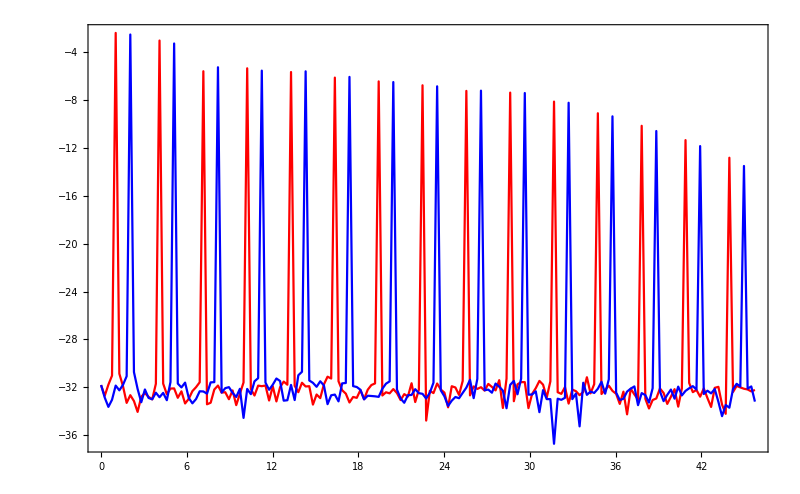

```mathematica
biColorSpectrum[Most[bicircularTest]]
```

### Bicircular fields with a sine-squared envelope

To benchmark the original calculations, we compared them with the output of full MCTDH calculations. Here we used a sin^2 envelope as the TDSE numerics require a finite pulse; the calculations take correspondingly longer but they are still very manageable (two/three minutes per calculation for a fifteen-cycle pulse, resolving up to ~70 harmonics). One distinctive feature is that the harmonics near the cutoff are broader, because less cycles contribute to those energies.

```mathematica
bicircularEnvelopeA[t_]:=cosPowerFlatTop[ω1,TotalCycles,2][t](F1/ω1{ Cos[t ω1] Sin[α],- Cos[α] Sin[t ω1]}+F2/ω2{Cos[β]Cos[ω2 t],Sin[β]Sin[ω2 t]});
bicircularParameters={F1->0.075,F2->0.075,α->45°,β->45°,ω1->45.6/800,ω2->45.6/400};
```

If (as in this case) the field depends on a number-of-cycles parameter, care must be taken that it matches the num option of the main call.

```mathematica
AbsoluteTiming[
bicircularEnvelopeDipole=makeDipoleList[VectorPotential->bicircularEnvelopeA,FieldParameters->Join[bicircularParameters,{TotalCycles->15}],PointsPerCycle->150,TotalCycles->15];
]
```

{141.302,Null}

Plotting the spectrum, and a zoom at the plateau:

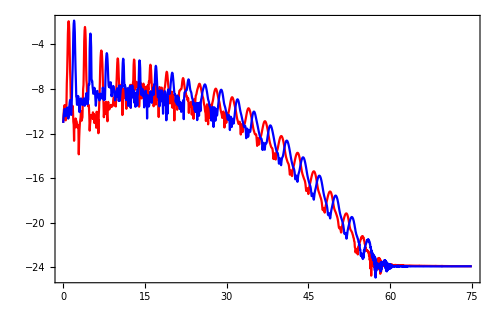

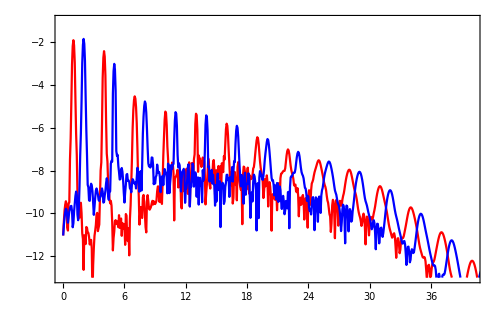

```mathematica
biColorSpectrum[bicircularEnvelopeDipole,PointsPerCycle->150,TotalCycles->15,ImageSize->500]
biColorSpectrum[bicircularEnvelopeDipole,PointsPerCycle->150,TotalCycles->15,ImageSize->500,PlotRange->{{0,40},{-13,-1}}]
```

The comparable MCTDH spectrum, for identical conditions, looks like this:

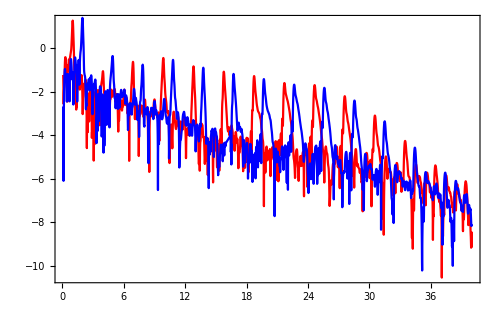

### Original RB-SFA: ‘rotating’ bicircular fields

#### Calculation

Here the fundamental laser driver has been set at an elliptical polarization (as in the original experiment, A. Fleischer et al., Nature Photon. 8, 543 (2014)), which helps investigate the spin-angular-momentum conservation properties of HHG. In the model proposed in the original paper (Phys. Rev. A 90, 043829 (2014)), the photon model is validated by splitting the elliptical field itself into two circular components, which can then be tuned independently:

```mathematica
rotatingBicircularA[t_]:=envelope[t](F2/ω2{Cos[β]Cos[ω2 t-ϕ1],Sin[β]Sin[ω2 t-ϕ1]}+F1/(√2)(1/ω1 Cos[α-π/4]{Cos[ω1 t+ϕ1],-Sin[ω1 t+ϕ1]}+1/((1+δ)ω1)Sin[α-π/4]{Cos[(1+δ)ω1 t-ϕ1+ϕ2],+Sin[(1+δ)ω1 t -ϕ1+ϕ2]}));
```

```mathematica
DistributeDefinitions["RBSFA`"];
directory=FileNameJoin[{NotebookDirectory[],"Temp Data"}];
filename[δ_]:=FileNameJoin[{directory,"data 25.09 detuning scan at δ="<>ToString[δ]<>".txt"}];
Length[δRange=Range[0,0.25,0.001]]
```

251

To test the validity of the photon model, we ran a scan over the detuning δ, using the calculation below.

```mathematica
DateString[]
Print["Total = ",Length[δRange]," points at ~230s/point will be done at approximately ",DateString[AbsoluteTime[]+Length[δRange]*230./7],"."]
ParallelTable[
Print[AbsoluteTiming[
makeDipoleList[
VectorPotential->rotatingBicircularA,
FieldParameters->{α->35 °,β->45 °,F1->0.075,F2->0.075,ω1->0.057,ω2->1.95×0.057,ϕ1->0,ϕ2->0,envelope->flatTopEnvelope[ω1,26,3]},
CarrierFrequency->0.057,TotalCycles->26,PointsPerCycle->115,nGate->1.8,PointNumberCorrection->1,Preintegrals->"Numeric",
ReportingFunction->Function[Write[filename[δ],#]]
];]];
Print[DateString[]];
,{δ,δRange}];
DateString[]
NotebookSave[]
```

Total time 2h 32min. (Desktop machine with 8-thread, 4-core Intel i7-3770 CPU at 3.40GHz, 16GB RAB, running 7 Mathematica kernels in parallel.)
Expand this cell to see the calculation log.

Fri 25 Sep 2015 23:54:59

Total = 251 points at ~230s/point will be done at approximately Sat 26 Sep 2015 02:12:26.

{243.449,Null}

Fri 25 Sep 2015 23:59:03

{254.907,Null}

Fri 25 Sep 2015 23:59:14

{256.794,Null}

Fri 25 Sep 2015 23:59:16

{257.342,Null}

Fri 25 Sep 2015 23:59:17

{257.439,Null}

{257.496,Null}

Fri 25 Sep 2015 23:59:17

Fri 25 Sep 2015 23:59:17

{258.157,Null}

Fri 25 Sep 2015 23:59:18

{256.621,Null}

Sat 26 Sep 2015 00:03:20

{257.176,Null}

Sat 26 Sep 2015 00:03:32

{256.457,Null}

Sat 26 Sep 2015 00:03:33

{257.858,Null}

Sat 26 Sep 2015 00:03:35

{257.249,Null}

Sat 26 Sep 2015 00:03:35

{258.549,Null}

Sat 26 Sep 2015 00:03:35

{262.01,Null}

Sat 26 Sep 2015 00:03:39

{257.52,Null}

Sat 26 Sep 2015 00:07:37

{255.313,Null}

Sat 26 Sep 2015 00:07:47

{257.303,Null}

Sat 26 Sep 2015 00:07:50

{256.504,Null}

Sat 26 Sep 2015 00:07:51

{256.676,Null}

Sat 26 Sep 2015 00:07:51

{257.886,Null}

Sat 26 Sep 2015 00:07:53

{258.438,Null}

Sat 26 Sep 2015 00:07:57

{259.005,Null}

Sat 26 Sep 2015 00:11:56

{255.526,Null}

Sat 26 Sep 2015 00:12:02

{255.989,Null}

Sat 26 Sep 2015 00:12:07

{257.398,Null}

Sat 26 Sep 2015 00:12:07

{258.373,Null}

Sat 26 Sep 2015 00:12:10

{259.41,Null}

Sat 26 Sep 2015 00:12:13

{257.386,Null}

Sat 26 Sep 2015 00:12:15

{253.567,Null}

Sat 26 Sep 2015 00:16:10

{256.773,Null}

Sat 26 Sep 2015 00:16:19

{256.932,Null}

Sat 26 Sep 2015 00:16:24

{258.164,Null}

Sat 26 Sep 2015 00:16:26

{255.857,Null}

Sat 26 Sep 2015 00:16:26

{256.819,Null}

Sat 26 Sep 2015 00:16:32

{260.329,Null}

Sat 26 Sep 2015 00:16:33

{257.695,Null}

Sat 26 Sep 2015 00:20:27

{254.694,Null}

Sat 26 Sep 2015 00:20:34

{257.262,Null}

Sat 26 Sep 2015 00:20:42

{256.648,Null}

Sat 26 Sep 2015 00:20:42

{258.688,Null}

Sat 26 Sep 2015 00:20:44

{257.148,Null}

Sat 26 Sep 2015 00:20:50

{260.138,Null}

Sat 26 Sep 2015 00:20:52

{255.577,Null}

Sat 26 Sep 2015 00:24:49

{262.37,Null}

Sat 26 Sep 2015 00:24:50

{255.263,Null}

Sat 26 Sep 2015 00:24:57

{256.929,Null}

Sat 26 Sep 2015 00:24:59

{260.329,Null}

Sat 26 Sep 2015 00:25:05

{254.807,Null}

Sat 26 Sep 2015 00:25:07

{257.474,Null}

Sat 26 Sep 2015 00:25:08

{254.524,Null}

Sat 26 Sep 2015 00:29:04

{257.08,Null}

Sat 26 Sep 2015 00:29:07

{256.669,Null}

Sat 26 Sep 2015 00:29:15

{258.81,Null}

Sat 26 Sep 2015 00:29:16

{253.721,Null}

Sat 26 Sep 2015 00:29:18

{254.744,Null}

Sat 26 Sep 2015 00:29:21

{254.037,Null}

Sat 26 Sep 2015 00:29:22

{254.339,Null}

Sat 26 Sep 2015 00:33:18

{255.706,Null}

Sat 26 Sep 2015 00:33:22

{249.275,Null}

Sat 26 Sep 2015 00:33:26

{252.394,Null}

Sat 26 Sep 2015 00:33:28

{253.764,Null}

Sat 26 Sep 2015 00:33:32

{252.286,Null}

Sat 26 Sep 2015 00:33:34

{253.999,Null}

Sat 26 Sep 2015 00:33:35

{251.872,Null}

Sat 26 Sep 2015 00:37:30

{251.841,Null}

Sat 26 Sep 2015 00:37:34

{250.071,Null}

Sat 26 Sep 2015 00:37:36

{252.216,Null}

Sat 26 Sep 2015 00:37:40

{250.313,Null}

Sat 26 Sep 2015 00:37:44

{252.188,Null}

Sat 26 Sep 2015 00:37:45

{253.911,Null}

Sat 26 Sep 2015 00:37:49

{252.658,Null}

Sat 26 Sep 2015 00:41:43

{249.291,Null}

Sat 26 Sep 2015 00:41:45

{251.75,Null}

Sat 26 Sep 2015 00:41:46

{253.848,Null}

Sat 26 Sep 2015 00:41:54

{250.81,Null}

Sat 26 Sep 2015 00:41:55

{253.741,Null}

Sat 26 Sep 2015 00:41:58

{252.087,Null}

Sat 26 Sep 2015 00:42:02

{251.429,Null}

Sat 26 Sep 2015 00:45:54

{250.527,Null}

Sat 26 Sep 2015 00:45:56

{252.765,Null}

Sat 26 Sep 2015 00:45:59

{251.482,Null}

Sat 26 Sep 2015 00:46:07

{254.13,Null}

Sat 26 Sep 2015 00:46:08

{250.409,Null}

Sat 26 Sep 2015 00:46:09

{252.258,Null}

Sat 26 Sep 2015 00:46:14

{249.626,Null}

Sat 26 Sep 2015 00:50:05

{252.681,Null}

Sat 26 Sep 2015 00:50:07

{252.079,Null}

Sat 26 Sep 2015 00:50:11

{250.28,Null}

Sat 26 Sep 2015 00:50:18

{252.295,Null}

Sat 26 Sep 2015 00:50:19

{251.678,Null}

Sat 26 Sep 2015 00:50:20

{253.414,Null}

Sat 26 Sep 2015 00:50:27

{248.014,Null}

Sat 26 Sep 2015 00:54:13

{251.171,Null}

Sat 26 Sep 2015 00:54:18

{252.743,Null}

Sat 26 Sep 2015 00:54:24

{248.42,Null}

Sat 26 Sep 2015 00:54:29

{252.651,Null}

Sat 26 Sep 2015 00:54:32

{254.747,Null}

Sat 26 Sep 2015 00:54:33

{256.036,Null}

Sat 26 Sep 2015 00:54:43

{248.918,Null}

Sat 26 Sep 2015 00:58:22

{250.23,Null}

Sat 26 Sep 2015 00:58:28

{253.976,Null}

Sat 26 Sep 2015 00:58:38

{252.674,Null}

Sat 26 Sep 2015 00:58:41

{251.011,Null}

Sat 26 Sep 2015 00:58:44

{253.237,Null}

Sat 26 Sep 2015 00:58:45

{254.193,Null}

Sat 26 Sep 2015 00:58:57

{248.801,Null}

Sat 26 Sep 2015 01:02:31

{249.892,Null}

Sat 26 Sep 2015 01:02:38

{253.766,Null}

Sat 26 Sep 2015 01:02:51

{250.716,Null}

Sat 26 Sep 2015 01:02:52

{252.986,Null}

Sat 26 Sep 2015 01:02:57

{253.294,Null}

Sat 26 Sep 2015 01:02:58

{254.339,Null}

Sat 26 Sep 2015 01:03:12

{249.249,Null}

Sat 26 Sep 2015 01:06:40

{254.651,Null}

Sat 26 Sep 2015 01:06:53

{251.019,Null}

Sat 26 Sep 2015 01:07:03

{251.432,Null}

Sat 26 Sep 2015 01:07:04

{252.609,Null}

Sat 26 Sep 2015 01:07:10

{255.379,Null}

Sat 26 Sep 2015 01:07:14

{252.54,Null}

Sat 26 Sep 2015 01:07:24

{250.084,Null}

Sat 26 Sep 2015 01:10:50

{253.436,Null}

Sat 26 Sep 2015 01:11:06

{251.095,Null}

Sat 26 Sep 2015 01:11:15

{253.333,Null}

Sat 26 Sep 2015 01:11:16

{250.522,Null}

Sat 26 Sep 2015 01:11:20

{253.204,Null}

Sat 26 Sep 2015 01:11:27

{252.571,Null}

Sat 26 Sep 2015 01:11:37

{249.371,Null}

Sat 26 Sep 2015 01:15:00

{253.51,Null}

Sat 26 Sep 2015 01:15:20

{254.336,Null}

Sat 26 Sep 2015 01:15:29

{253.652,Null}

Sat 26 Sep 2015 01:15:30

{256.302,Null}

Sat 26 Sep 2015 01:15:37

{252.93,Null}

Sat 26 Sep 2015 01:15:40

{253.634,Null}

Sat 26 Sep 2015 01:15:51

{251.119,Null}

Sat 26 Sep 2015 01:19:11

{252.183,Null}

Sat 26 Sep 2015 01:19:32

{251.577,Null}

Sat 26 Sep 2015 01:19:41

{254.152,Null}

Sat 26 Sep 2015 01:19:43

{252.267,Null}

Sat 26 Sep 2015 01:19:49

{254.025,Null}

Sat 26 Sep 2015 01:19:54

{251.914,Null}

Sat 26 Sep 2015 01:20:03

{252.455,Null}

Sat 26 Sep 2015 01:23:23

{252.665,Null}

Sat 26 Sep 2015 01:23:45

{252.913,Null}

Sat 26 Sep 2015 01:23:54

{251.737,Null}

Sat 26 Sep 2015 01:23:55

{252.655,Null}

Sat 26 Sep 2015 01:24:02

{254.643,Null}

Sat 26 Sep 2015 01:24:09

{254.561,Null}

Sat 26 Sep 2015 01:24:17

{251.304,Null}

Sat 26 Sep 2015 01:27:35

{252.381,Null}

Sat 26 Sep 2015 01:27:57

{250.912,Null}

Sat 26 Sep 2015 01:28:06

{253.389,Null}

Sat 26 Sep 2015 01:28:08

{254.54,Null}

Sat 26 Sep 2015 01:28:16

{252.447,Null}

Sat 26 Sep 2015 01:28:21

{250.941,Null}

Sat 26 Sep 2015 01:28:28

{251.042,Null}

Sat 26 Sep 2015 01:31:46

{253.258,Null}

Sat 26 Sep 2015 01:32:11

{253.693,Null}

Sat 26 Sep 2015 01:32:20

{255.796,Null}

Sat 26 Sep 2015 01:32:23

{252.292,Null}

Sat 26 Sep 2015 01:32:28

{251.498,Null}

Sat 26 Sep 2015 01:32:33

{253.874,Null}

Sat 26 Sep 2015 01:32:42

{250.817,Null}

Sat 26 Sep 2015 01:35:57

{254.017,Null}

Sat 26 Sep 2015 01:36:25

{250.89,Null}

Sat 26 Sep 2015 01:36:31

{254.441,Null}

Sat 26 Sep 2015 01:36:38

{251.566,Null}

Sat 26 Sep 2015 01:36:40

{254.02,Null}

Sat 26 Sep 2015 01:36:47

{253.733,Null}

Sat 26 Sep 2015 01:36:56

{248.917,Null}

Sat 26 Sep 2015 01:40:06

{252.298,Null}

Sat 26 Sep 2015 01:40:37

{253.614,Null}

Sat 26 Sep 2015 01:40:44

{252.666,Null}

Sat 26 Sep 2015 01:40:50

{255.123,Null}

Sat 26 Sep 2015 01:40:55

{252.493,Null}

Sat 26 Sep 2015 01:40:59

{255.39,Null}

Sat 26 Sep 2015 01:41:11

{248.751,Null}

Sat 26 Sep 2015 01:44:14

{253.427,Null}

Sat 26 Sep 2015 01:44:50

{250.359,Null}

Sat 26 Sep 2015 01:44:55

{255.603,Null}

Sat 26 Sep 2015 01:45:06

{252.843,Null}

Sat 26 Sep 2015 01:45:08

{254.434,Null}

Sat 26 Sep 2015 01:45:14

{253.936,Null}

Sat 26 Sep 2015 01:45:25

{249.489,Null}

Sat 26 Sep 2015 01:48:24

{254.609,Null}

Sat 26 Sep 2015 01:49:05

{252.49,Null}

Sat 26 Sep 2015 01:49:07

{252.409,Null}

Sat 26 Sep 2015 01:49:18

{254.696,Null}

Sat 26 Sep 2015 01:49:23

{253.177,Null}

Sat 26 Sep 2015 01:49:27

{255.789,Null}

Sat 26 Sep 2015 01:49:41

{248.62,Null}

Sat 26 Sep 2015 01:52:33

{254.66,Null}

Sat 26 Sep 2015 01:53:20

{253.74,Null}

Sat 26 Sep 2015 01:53:21

{253.78,Null}

Sat 26 Sep 2015 01:53:32

{251.811,Null}

Sat 26 Sep 2015 01:53:35

{254.042,Null}

Sat 26 Sep 2015 01:53:41

{253.371,Null}

Sat 26 Sep 2015 01:53:54

{249.143,Null}

Sat 26 Sep 2015 01:56:42

{254.544,Null}

Sat 26 Sep 2015 01:57:35

{255.728,Null}

Sat 26 Sep 2015 01:57:36

{253.229,Null}

Sat 26 Sep 2015 01:57:46

{257.017,Null}

Sat 26 Sep 2015 01:57:52

{252.004,Null}

Sat 26 Sep 2015 01:57:53

{254.533,Null}

Sat 26 Sep 2015 01:58:09

{252.019,Null}

Sat 26 Sep 2015 02:00:54

{251.881,Null}

Sat 26 Sep 2015 02:01:47

{252.105,Null}

Sat 26 Sep 2015 02:01:48

{251.961,Null}

Sat 26 Sep 2015 02:01:58

{252.435,Null}

Sat 26 Sep 2015 02:02:04

{253.186,Null}

Sat 26 Sep 2015 02:02:06

{254.602,Null}

Sat 26 Sep 2015 02:02:23

{251.084,Null}

Sat 26 Sep 2015 02:05:05

{250.27,Null}

Sat 26 Sep 2015 02:05:58

{252.045,Null}

Sat 26 Sep 2015 02:06:00

{254.221,Null}

Sat 26 Sep 2015 02:06:12

{255.596,Null}

Sat 26 Sep 2015 02:06:20

{253.951,Null}

Sat 26 Sep 2015 02:06:20

{255.577,Null}

Sat 26 Sep 2015 02:06:39

{247.568,Null}

Sat 26 Sep 2015 02:09:12

{252.734,Null}

Sat 26 Sep 2015 02:10:10

{252.616,Null}

Sat 26 Sep 2015 02:10:12

{254.627,Null}

Sat 26 Sep 2015 02:10:27

{252.523,Null}

Sat 26 Sep 2015 02:10:32

{252.796,Null}

Sat 26 Sep 2015 02:10:33

{255.219,Null}

Sat 26 Sep 2015 02:10:54

{251.551,Null}

Sat 26 Sep 2015 02:13:24

{251.664,Null}

Sat 26 Sep 2015 02:14:22

{253.936,Null}

Sat 26 Sep 2015 02:14:26

{252.518,Null}

Sat 26 Sep 2015 02:14:39

{253.397,Null}

Sat 26 Sep 2015 02:14:46

{254.648,Null}

Sat 26 Sep 2015 02:14:48

{253.289,Null}

Sat 26 Sep 2015 02:15:08

{252.79,Null}

Sat 26 Sep 2015 02:17:37

{252.897,Null}

Sat 26 Sep 2015 02:18:35

{256.919,Null}

Sat 26 Sep 2015 02:18:43

{253.88,Null}

Sat 26 Sep 2015 02:18:53

{251.461,Null}

Sat 26 Sep 2015 02:18:57

{255.058,Null}

Sat 26 Sep 2015 02:19:03

{254.171,Null}

Sat 26 Sep 2015 02:19:22

{250.378,Null}

Sat 26 Sep 2015 02:21:47

{255.346,Null}

Sat 26 Sep 2015 02:22:50

{255.272,Null}

Sat 26 Sep 2015 02:22:58

{254.574,Null}

Sat 26 Sep 2015 02:23:08

{253.245,Null}

Sat 26 Sep 2015 02:23:10

{256.747,Null}

Sat 26 Sep 2015 02:23:19

{255.07,Null}

Sat 26 Sep 2015 02:23:37

{241.296,Null}

Sat 26 Sep 2015 02:25:48

{237.181,Null}

Sat 26 Sep 2015 02:26:47

{235.884,Null}

Sat 26 Sep 2015 02:26:54

{230.584,Null}

Sat 26 Sep 2015 02:26:58

{228.565,Null}

Sat 26 Sep 2015 02:26:59

{226.844,Null}

Sat 26 Sep 2015 02:27:06

Sat 26 Sep 2015 02:27:06

The results can be pulled in from the files using this:

```mathematica
Do[detunedDipole[δ]=ReadList[filename[δ]],{δ,δRange}]
```

Or saved into a single location using this:

```mathematica
Save[FileNameJoin[{NotebookDirectory[],"Detuning scan collected data.txt"}],detunedDipole]
```

```mathematica
DumpSave[FileNameJoin[{NotebookDirectory[],"Detuning scan collected data.mx"}],detunedDipole];
```

and pulled in from the single location using this:

```mathematica
<<(FileNameJoin[{NotebookDirectory[],"Detuning scan collected data.txt"}]);
```

A sample spectrum looks like this:

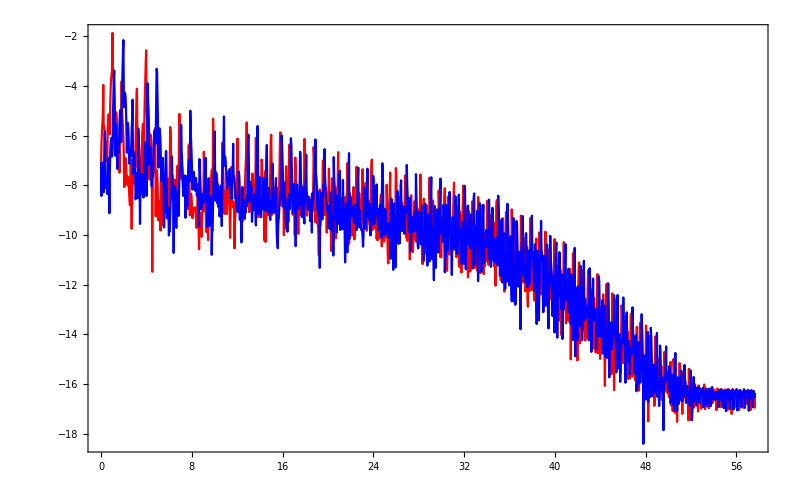

```mathematica
biColorSpectrum[detunedDipole[0.001RandomInteger[{0,1000}]],CarrierFrequency->45.6/800,TotalCycles->3,PointsPerCycle->115]
```

#### Plots from the original paper

The plots from the original paper were produced using the code below. For simplicity we pre-define an interpolation function.

```mathematica
conditions:=Sequence[CarrierFrequency->45.6/800,TotalCycles->26,PointsPerCycle->115]
```

```mathematica
Remove[detuningInterpolation]
With[{length=Length[getSpectrum[detunedDipole[0.],Polarization->{1,ⅈ}]]},
AbsoluteTiming[
Table[
detuningInterpolation[ϵ]=Interpolation[
Flatten[Table[
{{
harmonicOrderAxis[TargetLength->length,conditions],
Table[δ,{length}]
}ᵀ,
Log[10,getSpectrum[detunedDipole[δ],Polarization->{1,ϵ ⅈ}]]
}ᵀ
,{δ,δRange}],1]]
,{ϵ,{1,-1}}];
]
]
```

{2.99829,Null}

Some plotting admin:

```mathematica
CMRmap=Function[x,Blend[{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},x]];
CMRwithMin[minIn_,minOut_:1./9]:=Function[x,CMRmap[If[x<minIn,minOut/minIn x,minOut+(1-minOut)(x-minIn)/(1-minIn)]]]
min=6. 10^-9;
max=5. 10^-7;
colorfunction=CMRwithMin[min/max];
HOTicks[ϵ_]:=({#,If[ϵ==1,Style[#,Black],""],{0.02,0},{Thickness[0.005],Gray}}&/@Range[12,18,1])~Join~({#,"",{0.01,0},{Thickness[0.004],Gray}}&/@Range[11+1/2,18+1/4,1/4])
downTicks={{0,Style[0,Black],0},{0.25,Style[0.25,Black],0}}~Join~({#,Style[#,Black],{0.015,0},{Thickness[0.005],Gray}}&/@Range[0.05,0.20,0.05])~Join~({#,"",{0.01,0},{Thickness[0.004],Gray}}&/@Range[0.01,0.24,0.01]);
upTicks=({#,"",{0.015,0},{Thickness[0.005],Gray}}&/@Range[0.05,0.20,0.05])~Join~({#,"",{0.01,0},{Thickness[0.004],Gray}}&/@Range[0.01,0.24,0.01]);
```

The plot itself:

```mathematica
Row[Table[
splittingsScan[ϵ]=RegionPlot[
True
,{δ,0,0.25},{HO,11.25,18.5}
,AspectRatio->1.2
,PlotRangePadding->None
,ImagePadding->1{{35+15ϵ,20},{70,6}}
,ImageSize->{Automatic,550}
,PlotPoints->600
,FrameStyle->Automatic
,FrameLabel->{Style["ω'/ω-1",Black,12],If[ϵ==1,Style["Harmonic Order",Black,16],""]}
,ColorFunctionScaling->False
,FrameTicks->{{HOTicks[1],HOTicks[-1]},{downTicks,upTicks}}
,ColorFunction->Function[{δ,HO},colorfunction[(10^detuningInterpolation[ϵ][HO,δ])/max]]
,PlotLabel->Style[StringJoin[ϵ/.{1->"Right",-1->"Left"},"-circular harmonics"],Black,16]
]
,{ϵ,{1,-1}}]
]
```

(Removed to keep file size low.)